# Tecnológico de Monterrey Campus Toluca

## Métodos Numéricos: Primera Evaluación

Nombre y Matrícula: Mario Jacob García Navarro - A01363206

"Apegándome al Código de Ética de los Estudiantes del Tecnológico de Monterrey, me comprometo a que mi actuación en este examen esté regida por la honestidad académica."

________________________________
Firma

Datos: Fecha: 17 de junio 2011;  Verano 2014;

Instrucciones:

La implemenatación tiene un  valor de 100 pts.

Se calificará algoritmo, tablas, implementacion y gráfica de los problemas.

## Escenario

```mathematica
Import["http://mahtblog.files.wordpress.com/2011/03/foco.png?w=788"]
```

-Graphics-

Obtener puntos clave de la figura para conseguir el perfil de ésta.

Graficar los puntos (Corregir la altura con respecto al eje de rotación x).

Generar el perfil del foco “f(x)” utilizando Splines.

Graficar la función f(x) y los puntos tomados.

Calcular el área bajo la curva (Trapecios, Riemann y Simpson) y generar la tabla de los métodos con su respectivo error relativo absoluto.

Calcular la longitud de arco. (Trapecios, Riemann y Simpson) y generar la tabla de los métodos con su respectivo error relativo absoluto.

Graficar el sólido de revolución.

Calcular el volumen (Trapecios, Riemann y Simpson) y generar la tabla de los métodos con su respectivo error relativo absoluto.

## Obtener puntos clave de la figura para conseguir el perfil de ésta.

```mathematica
puntos={{18.3148,133.872},{20.9311,149.57},{52.3279,179.005},{58.8689,178.351},{63.4475,182.93},{69.3344,179.005},{78.4918,182.93},{88.3033,179.005},{93.5361,182.93},{102.039,179.005},{108.58,183.584},{120.354,183.584},{142.593,194.049},{151.751,196.666},{185.764,203.207},{213.236,218.905},{248.557,236.566},{274.721,241.798},{314.621,235.911},{347.326,220.213},{368.911,198.628},{385.264,167.885},{389.843,145.646},{390.497,132.564}};
```

## Graficar los puntos (Corregir la altura con respecto al eje de rotación x).

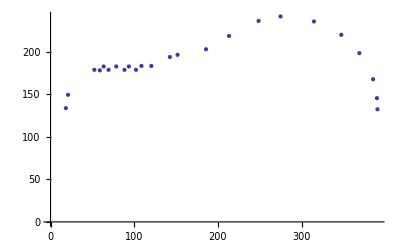

```mathematica
ListPlot[puntos,AspectRatio->Automatic,AxesOrigin->{0, 0}]
```

Tratamiento a los puntos (Se le resta la altura más baja a todas las demás).

```mathematica
puntosTratados=Table[{puntos[[i,1]],puntos[[i,2]]-puntos[[1,2]]},{i,1,Length[puntos]}]
```

{{18.3148,0.},{20.9311,15.698},{52.3279,45.133},{58.8689,44.479},{63.4475,49.058},{69.3344,45.133},{78.4918,49.058},{88.3033,45.133},{93.5361,49.058},{102.039,45.133},{108.58,49.712},{120.354,49.712},{142.593,60.177},{151.751,62.794},{185.764,69.335},{213.236,85.033},{248.557,102.694},{274.721,107.926},{314.621,102.039},{347.326,86.341},{368.911,64.756},{385.264,34.013},{389.843,11.774},{390.497,-1.308}}

Se grafican los puntos tratados para comprobar que realemente se encuentran tocando el eje.

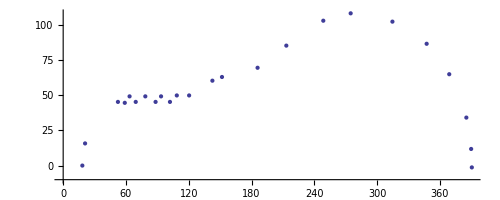

```mathematica
ListPlot[puntosTratados,AspectRatio->Automatic,AxesOrigin->{0, -10}]
```

## Generar el perfil del foco “f(x)” utilizando Splines.

Se generan las “x”, las alturas y las “h” para los Splines

```mathematica
x[j_]:=puntosTratados[[j+1,1]]
```

```mathematica
a[j_]:=puntosTratados[[j+1,2]]
```

```mathematica
h[j_]:=x[j+1]-x[j]
```

Se comprueba la independencia de las funciones

```mathematica
ListPlot[
Table[{x[i],a[i]},{i,0,Length[puntosTratados]-1}],AspectRatio->Automatic, AxesOrigin->{0, -10}]
```

-Graphics-

Se encuentran las dimensiones de los puntos para posteriormente, generar la matriz (Renglones: n-1, Columnas: n+1)

```mathematica
Dimensions[puntosTratados]
```

{24,2}

```mathematica
m=({{h[0], 2 (h[0]+h[1]), h[1], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, h[1], 2 (h[1]+h[2]), h[2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, h[2], 2 (h[2]+h[3]), h[3], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, h[3], 2 (h[3]+h[4]), h[4], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, h[4], 2 (h[4]+h[5]), h[5], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, h[5], 2 (h[5]+h[6]), h[6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, h[6], 2 (h[6]+h[7]), h[7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, h[7], 2 (h[7]+h[8]), h[8], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, h[8], 2 (h[8]+h[9]), h[9], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, h[9], 2 (h[9]+h[10]), h[10], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[10], 2 (h[10]+h[11]), h[11], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[11], 2 (h[11]+h[12]), h[12], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[12], 2 (h[12]+h[13]), h[13], 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[13], 2 (h[13]+h[14]), h[14], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[14], 2 (h[14]+h[15]), h[15], 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[15], 2 (h[15]+h[16]), h[16], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[16], 2 (h[16]+h[17]), h[17], 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[17], 2 (h[17]+h[18]), h[18], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[18], 2 (h[18]+h[19]), h[19], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[19], 2 (h[19]+h[20]), h[20], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[20], 2 (h[20]+h[21]), h[21], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[21], 2 (h[21]+h[22]), h[22]}});
```

Se generan los resultados y posteriormente se incluyen en una lista

```mathematica
s=Table[3/h[j-1](a[j-1]-a[j])+3/h[j](a[j+1]-a[j]),{j,1,22}];
```

```mathematica
results=LinearSolve[m,s]
```

```mathematica
{-0.010492668678247719,-0.24182295263605932,0.041089122259109725,0.20827139021827465,-0.3495253627173531,0.2313370447103914,-0.17657170987247253,0.21345652844465782,-0.2369330267074531,0.20661840737018614,-0.10963403787759148,0.047924767386415594,-0.025072615885292894,-0.0α05002726574810504`,0.011207586918916795,-0.002573936372839203,-0.005629979347978847,-0.004468033546139415,-0.007641221398724446,0.008883185090489076,-0.10538182918310748,0.31580294322564,-4.461191222725918,-0.2969370263946776}
```

Se determinan las funciones de “c”, d“” y “b”

```mathematica
c[j_]:=results[[j+1]]
```

```mathematica
d[j_]:=(c[j+1]-c[j])/(3 h[j])
```

```mathematica
b[j_]:=1/h[j](a[j+1]-a[j]-h[j]^2/3(2 c[j]+c[j+1]))
```

Se genera la función por partes

```mathematica
f[t_]:=Piecewise[Table[{a[i]+b[i](t-x[i])+c[i](t-x[i])^2+d[i](t-x[i])^3,x[i]<t<x[i+1]},{i,0,22}]]
```

```mathematica
funcion[t_]:=Piecewise[{{0.+6.229271553535395 (-18.3148+t)-0.010492668678247719 (-18.3148+t)^2-0.029472955950236555 (-18.3148+t)^3, 18.3148<t<20.9311}, {15.697999999999979+5.569138193490775 (-20.9311+t)-0.24182295263605932 (-20.9311+t)^2+0.003003618998275505 (-20.9311+t)^3, 20.9311<t<52.3279}, {45.13299999999998-0.7332617320882332 (-52.3279+t)+0.041089122259109725 (-52.3279+t)^2+0.008519709930141416 (-52.3279+t)^3, 52.3279<t<58.8689}, {44.478999999999985+0.8978053800263373 (-58.8689+t)+0.20827139021827465 (-58.8689+t)^2-0.040608974572695265 (-58.8689+t)^3, 58.8689<t<63.4475}, {49.05799999999999+0.251059941542055 (-63.4475+t)-0.3495253627173531 (-63.4475+t)^2+0.03289011236404809 (-63.4475+t)^3, 63.4475<t<69.3344}, {45.13299999999998-0.4447028677331299 (-69.3344+t)+0.2313370447103914 (-69.3344+t)^2-0.01484805565563967 (-69.3344+t)^3, 69.3344<t<78.4918}, {49.05799999999999+0.05680520951162752 (-78.4918+t)-0.17657170987247253 (-78.4918+t)^2+0.013250717298310845 (-78.4918+t)^3, 78.4918<t<88.3033}, {45.13299999999998+0.41870060693262534 (-88.3033+t)+0.21345652844465782 (-88.3033+t)^2-0.028690156649856666 (-88.3033+t)^3, 88.3033<t<93.5361}, {49.05799999999999+0.2958527868230717 (-93.5361+t)-0.2369330267074531 (-93.5361+t)^2+0.01738824142655797 (-93.5361+t)^3, 93.5361<t<102.039}, {45.13299999999998+0.03809061006022419 (-102.039+t)+0.20661840737018614 (-102.039+t)^2-0.01611641671751403 (-102.039+t)^3, 102.039<t<108.58}, {49.71199999999999+0.6724653709112889 (-108.58+t)-0.10963403787759148 (-108.58+t)^2+0.004460642241775863 (-108.58+t)^3, 108.58<t<120.354}, {49.71199999999999-0.05409957985181614 (-120.354+t)+0.047924767386415594 (-120.354+t)^2-0.0010941346773941953 (-120.354+t)^3, 120.354<t<142.593}, {60.17699999999999+0.454109417381652 (-142.593+t)-0.025072615885292894 (-142.593+t)^2+0.0007305048158434286 (-142.593+t)^3, 142.593<t<151.751}, {62.79399999999998+0.17867943113203177 (-151.751+t)-0.005002726574810504 (-151.751+t)^2+0.00015886390001594778 (-151.751+t)^3, 151.751<t<185.764}, {69.33499999999998+0.38972534601611314 (-185.764+t)+0.011207586918916795 (-185.764+t)^2-0.00016721902654528257 (-185.764+t)^3, 185.764<t<213.236}, {85.03299999999999+0.6269089938179573 (-213.236+t)-0.002573936372839203 (-213.236+t)^2-0.00002884066112831502 (-213.236+t)^3, 213.236<t<248.557}, {102.69399999999999+0.3371384866429392 (-248.557+t)-0.005629979347978847 (-248.557+t)^2+0.000014803365971556745 (-248.557+t)^3, 248.557<t<274.721}, {107.92599999999999+0.07293407728122055 (-274.721+t)-0.004468033546139415 (-274.721+t)^2-0.000026509505869549148 (-274.721+t)^3, 274.721<t<314.621}, {102.03899999999999-0.41022519501883786 (-314.621+t)-0.007641221398724446 (-314.621+t)^2+0.0001684187584896652 (-314.621+t)^3, 314.621<t<347.326}, {86.34099999999998-0.3696067724796814 (-347.326+t)+0.008883185090489076 (-347.326+t)^2-0.0017645743845818341 (-347.326+t)^3, 347.326<t<368.911}, {64.75599999999997-2.4525300052188563 (-368.911+t)-0.10538182918310748 (-368.911+t)^2+0.008585270233978419 (-368.911+t)^3, 368.911<t<385.264}, {34.01299999999998+0.9884864727186876 (-385.264+t)+0.31580294322564 (-385.264+t)^2-0.3477465360669397 (-385.264+t)^3, 385.264<t<389.843}, {11.773999999999972-17.993246459113106 (-389.843+t)-4.461191222725918 (-389.843+t)^2+2.1224537188232744 (-389.843+t)^3, 389.843<t<390.497}, {0, True}}]
```

## Graficar la función f(x) y los puntos tomados.

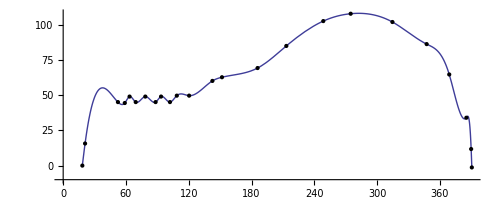

```mathematica
Plot[funcion[t],{t,x[0],x[23]},AspectRatio->Automatic,Epilog->Map[Point,puntosTratados],AxesOrigin->{0,-10}]
```

## Calcular el área bajo la curva (Trapecios, Riemann y Simpson) y generar la tabla de los métodos con su respectivo error relativo absoluto.

Generar los distintos métodos de integración

```mathematica
metodoTrapecio[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=1,i≤ n-1,i++,
sum =sum+funcion[a+i*h];];
Return[h/2(funcion[a]+funcion[b])+h*sum];
];
```

```mathematica
(** Suma Inferior **)
```

```mathematica
sumaInferior[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=0,i≤ n-1,i++,
sum =sum+h*funcion[a+i*h];];
Return[sum];
];
```

```mathematica
(** Suma Superior **)
```

```mathematica
sumaSuperior[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=1,i≤ n,i++,
sum =sum+h*funcion[a+i*h];];
Return[sum];
];
```

```mathematica
simpson[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/(2*n);
sumPar = 0;
For[i=1,i≤ n-1,i++,
sumPar =sumPar+funcion[a+i*h*2];];
sumImpar = 0;
For[i=1,i≤ n,i++,
sumImpar =sumImpar+funcion[a+h*(2*i-1)];];
Return[h/3(funcion[a]+funcion[b]+2*sumPar+4*sumImpar)];
];
```

Construir una tabla comparativa entre los distintos métodos

```mathematica
TableForm[
Table[{i,NIntegrate[funcion[y],{y,x[0],x[23]}],
NumberForm[metodoTrapecio[x[0],x[23],i],{10,10}],NumberForm[sumaInferior[x[0],x[23],i],{10,10}],NumberForm[sumaSuperior[x[0],x[23],i],{10,10}],
NumberForm[simpson[x[0],x[23],i],{10,10}],
Abs[(NIntegrate[funcion[y],{y,x[0],x[23]}]-metodoTrapecio[x[0],x[23],i])/NIntegrate[funcion[y],{y,x[0],x[23]}]*100],Abs[(NIntegrate[funcion[y],{y,x[0],x[23]}]-sumaInferior[x[0],x[23],i])/NIntegrate[funcion[y],{y,x[0],x[23]}]*100],Abs[(NIntegrate[funcion[y],{y,x[0],x[23]}]-sumaSuperior[x[0],x[23],i])/NIntegrate[funcion[y],{y,x[0],x[23]}]*100],Abs[(NIntegrate[funcion[y],{y,x[0],x[23]}]-simpson[x[0],x[23],i])/NIntegrate[funcion[y],{y,x[0],x[23]}]*100]},{i,1,6}],TableHeadings->{None,{"Índice","Valor Real", "Método de Trapecio", "Suma Inferior (Riemann)","Suma Superior (Riemann)","Método de Simpson","E.V.R.P. Método de Trapecio","E.V.R.P. Suma Inferior","E.V.R.P. Suma Superior","E.V.R.P. Método de Simpson"}}]
```

Índice | Valor Real | Método de Trapecio | Suma Inferior (Riemann) | Suma Superior (Riemann) | Método de Simpson | E.V.R.P. Método de Trapecio | E.V.R.P. Suma Inferior | E.V.R.P. Suma Superior | E.V.R.P. Método de Simpson
1 | 26840.5 | 0.0000000000 | 0.0000000000 | 0.0000000000 | 19703.7642900000 | 100. | 100. | 100. | 26.5894
2 | 26840.5 | 14777.8232200000 | 14777.8232200000 | 14777.8232200000 | 24501.9841500000 | 44.942 | 44.942 | 44.942 | 8.71258
3 | 26840.5 | 20728.5317100000 | 20728.5317100000 | 20728.5317100000 | 25385.8134100000 | 22.7714 | 22.7714 | 22.7714 | 5.41968
4 | 26840.5 | 22070.9439200000 | 22070.9439200000 | 22070.9439200000 | 26195.2036800000 | 17.7699 | 17.7699 | 17.7699 | 2.40413
5 | 26840.5 | 23459.9084500000 | 23459.9084500000 | 23459.9084500000 | 26070.7668200000 | 12.5951 | 12.5951 | 12.5951 | 2.86774
6 | 26840.5 | 24221.4929800000 | 24221.4929800000 | 24221.4929800000 | 26628.8462900000 | 9.75761 | 9.75761 | 9.75761 | 0.788497

## Calcular la longitud de arco. (Trapecios, Riemann y Simpson) y generar la tabla de los métodos con su respectivo error relativo absoluto.

Encontrar la derivada de la función

```mathematica
der[x_]:=D[funcion[t],t]/.t->x
```

Establecer la función de longitud de arco junto con sus métodos de integración

```mathematica
longitudArco[x_]:=Sqrt[1+(der[x])^2]
```

```mathematica
metodoTrapecioArco[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=1,i≤ n-1,i++,
sum =sum+longitudArco[a+i*h];];
Return[h/2(longitudArco[a]+longitudArco[b])+h*sum];
];
```

```mathematica
(** Suma Inferior **)
```

```mathematica
sumaInferiorArco[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=0,i≤ n-1,i++,
sum =sum+h*longitudArco[a+i*h];];
Return[sum];
];
```

```mathematica
(** Suma Superior **)
```

```mathematica
sumaSuperiorArco[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=1,i≤ n,i++,
sum =sum+h*longitudArco[a+i*h];];
Return[sum];
];
```

```mathematica
simpsonArco[a0_,b0_,n0_]:=Module[{a=a0,b=b0,n=n0,i},
h=(b-a)/(2*n);
sumPar = 0;
For[i=1,i≤ n-1,i++,
sumPar =sumPar+longitudArco[a+i*h*2];];
sumImpar = 0;
For[i=1,i≤ n,i++,
sumImpar =sumImpar+longitudArco[a+h*(2*i-1)];];
Return[h/3(longitudArco[a]+longitudArco[b]+2*sumPar+4*sumImpar)];
];
```

```mathematica
TableForm[
Monitor[Table[{i,NIntegrate[longitudArco[y],{y,x[0],x[23]}],
NumberForm[metodoTrapecioArco[18.314,390.49,i],{10,10}],NumberForm[sumaInferiorArco[18.314,390.49,i],{10,10}],NumberForm[sumaSuperiorArco[18.314,390.49,i],{10,10}],
NumberForm[simpsonArco[18.314,390.49,i],{10,10}],
Abs[(NIntegrate[longitudArco[y],{y,18.314,390.49}]-metodoTrapecioArco[18.314,390.49,i])/NIntegrate[longitudArco[y],{y,18.314,390.49}]*100],Abs[(NIntegrate[longitudArco[y],{y,18.314,390.49}]-sumaInferiorArco[18.314,390.49,i])/NIntegrate[longitudArco[y],{y,18.314,390.49}]*100],Abs[(NIntegrate[longitudArco[y],{y,18.314,390.49}]-sumaSuperiorArco[18.314,390.49,i])/NIntegrate[longitudArco[y],{y,18.314,390.49}]*100],Abs[(NIntegrate[longitudArco[y],{y,18.314,x[23]}]-simpsonArco[18.314,390.49,i])/NIntegrate[longitudArco[y],{y,18.314,390.49}]*100]},{i,1,6}],Row[{ProgressIndicator[i,{1,6}],i},""]],TableHeadings->{None,{"Índice","Valor Real", "Método de Trapecio", "Suma Inferior (Riemann)","Suma Superior (Riemann)","Método de Simpson","E.V.R.P. Método de Trapecio","E.V.R.P. Suma Inferior","E.V.R.P. Suma Superior","E.V.R.P. Método de Simpson"}}]
```

Índice | Valor Real | Método de Trapecio | Suma Inferior (Riemann) | Suma Superior (Riemann) | Método de Simpson | E.V.R.P. Método de Trapecio | E.V.R.P. Suma Inferior | E.V.R.P. Suma Superior | E.V.R.P. Método de Simpson
1 | 509.943 | 4117.0622610000 | 372.1760000000 | 7861.9485230000 | 1666.0340570000 | 707.59 | 26.9951 | 1442.18 | 226.775
2 | 509.943 | 2278.7911080000 | 406.3479774000 | 4151.2342390000 | 1011.2295600000 | 347.001 | 20.292 | 714.293 | 98.3307
3 | 509.943 | 1634.6168540000 | 386.3214339000 | 2882.9122750000 | 827.2379679000 | 220.641 | 24.2204 | 465.503 | 62.2394
4 | 509.943 | 1328.1199470000 | 391.8983819000 | 2264.3415130000 | 707.8038447000 | 160.52 | 23.1264 | 344.166 | 38.8116
5 | 509.943 | 1147.4901400000 | 398.5128873000 | 1896.4673920000 | 652.9791671000 | 125.088 | 21.8289 | 272.005 | 28.0574
6 | 509.943 | 1029.0826890000 | 404.9349793000 | 1653.2304000000 | 626.8725338000 | 101.862 | 20.5692 | 224.293 | 22.9364

## Graficar el sólido de revolución.

```mathematica
RevolutionPlot3D[{funcion[x],x },{x,x[0],x[23]},{θ,-Pi,Pi},Mesh-> False,Boxed->False,Axes->True, Background-> White,PerformanceGoal->"Quality", PlotStyle-> Directive[Yellow, Specularity[Blue, 20]]]
```

-Graphics3D-

## Calcular el volumen (Trapecios, Riemann y Simpson) y generar la tabla de los métodos con su respectivo error relativo absoluto.

```mathematica
vol[x_]:=Pi*(funcion[x])^2
```

```mathematica
metodoTrapecioVolumen[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=1,i≤ n-1,i++,
sum =sum+vol[a+i*h];];
Return[h/2(vol[a]+vol[b])+h*sum];
];
```

```mathematica
(** Suma Inferior **)
```

```mathematica
sumaInferiorVolumen[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=0,i≤ n-1,i++,
sum =sum+h*vol[a+i*h];];
Return[sum];
];
```

```mathematica
(** Suma Superior **)
```

```mathematica
sumaSuperiorVolumen[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=1,i≤ n,i++,
sum =sum+h*vol[a+i*h];];
Return[sum];
];
```

```mathematica
simpsonVolumen[a0_,b0_,n0_]:=Module[{a=a0,b=b0,n=n0,i},
h=(b-a)/(2*n);
sumPar = 0;
For[i=1,i≤ n-1,i++,
sumPar =sumPar+vol[a+i*h*2];];
sumImpar = 0;
For[i=1,i≤ n,i++,
sumImpar =sumImpar+vol[a+h*(2*i-1)];];
Return[h/3(vol[a]+vol[b]+2*sumPar+4*sumImpar)];
];
```

```mathematica
TableForm[
Table[{i,NIntegrate[vol[y],{y,x[0],x[23]}],
NumberForm[metodoTrapecioVolumen[18.314,390.49,i],{10,10}],NumberForm[sumaInferiorVolumen[18.314,390.49,i],{10,10}],NumberForm[sumaSuperiorVolumen[18.314,390.49,i],{10,10}],
NumberForm[simpsonVolumen[18.314,390.49,i],{10,10}],
Abs[(NIntegrate[vol[y],{y,18.314,390.49}]-metodoTrapecioVolumen[18.314,390.49,i])/NIntegrate[vol[y],{y,18.314,390.49}]*100],Abs[(NIntegrate[vol[y],{y,18.314,390.49}]-sumaInferiorVolumen[18.314,390.49,i])/NIntegrate[vol[y],{y,18.314,390.49}]*100],Abs[(NIntegrate[vol[y],{y,18.314,390.49}]-sumaSuperiorVolumen[18.314,390.49,i])/NIntegrate[vol[y],{y,18.314,390.49}]*100],Abs[(NIntegrate[vol[y],{y,18.314,390.49}]-simpsonVolumen[18.314,390.49,i])/NIntegrate[vol[y],{y,18.314,390.49}]*100]},{i,1,6}],TableHeadings->{None,{"Índice","Valor Real", "Método de Trapecio", "Suma Inferior (Riemann)","Suma Superior (Riemann)","Método de Simpson","E.V.R.P. Método de Trapecio","E.V.R.P. Suma Inferior","E.V.R.P. Suma Superior","E.V.R.P. Método de Simpson"}}]
```

Índice | Valor Real | Método de Trapecio | Suma Inferior (Riemann) | Suma Superior (Riemann) | Método de Simpson | E.V.R.P. Método de Trapecio | E.V.R.P. Suma Inferior | E.V.R.P. Suma Superior | E.V.R.P. Método de Simpson
1 | 6.79429×10^6 | 787.0344360000 | 0.0000000000 | 1574.0688720000 | 4.9155585300×10^6 | 99.9884 | 100. | 99.9768 | 27.6516
2 | 6.79429×10^6 | 3.6868656560×10^6 | 3.6864721390×10^6 | 3.6872591730×10^6 | 6.6951410280×10^6 | 45.7358 | 45.7416 | 45.73 | 1.45928
3 | 6.79429×10^6 | 5.8695258050×10^6 | 5.8692634600×10^6 | 5.8697881500×10^6 | 6.5716879590×10^6 | 13.6109 | 13.6147 | 13.607 | 3.27629
4 | 6.79429×10^6 | 5.9430721850×10^6 | 5.9428754260×10^6 | 5.9432689440×10^6 | 6.8210617260×10^6 | 12.5284 | 12.5313 | 12.5255 | 0.394049
5 | 6.79429×10^6 | 6.2898031870×10^6 | 6.2896457800×10^6 | 6.2899605940×10^6 | 6.7322443230×10^6 | 7.42514 | 7.42746 | 7.42283 | 0.913187
6 | 6.79429×10^6 | 6.3961474200×10^6 | 6.3960162480×10^6 | 6.3962785930×10^6 | 6.8761504830×10^6 | 5.85994 | 5.86187 | 5.85801 | 1.20486